```mathematica
wtbs[max_,a_,b_,d_,g_,more_]:=Module[
{zetaPool,i},
zetaPool = ConstantArray[0,more];
zetaPool[[1]] = a;
For[i=2, i≤more, i++,
zetaPool[[i]] = zetaPool[[i - 1]] * (b * (1+(g * (i/max)^(d))));
];
zetaPool
]
```

```mathematica
maxFun=36;
a=0.019988028;
b=1.8373057;
d=5.0736518;
g=1.5766373;
wtbs[maxFun,a,b,d,g,maxFun+1]
```

{0.019988,0.0367241,0.0674738,0.123973,0.227792,0.418598,0.769391,1.41469,2.60283,4.79354,8.84109,16.341,30.293,56.3856,105.521,198.868,378.18,727.364,1418.7,2814.87,5701.09,11832.1,25269.1,55782.8,127896.,306059.,768304.,2.03346×10^6,5.70265×10^6,1.70277×10^7,5.43835×10^7,1.86585×10^8,6.90402×10^8,2.76495×10^9,1.20228×10^10,5.69165×10^10,2.94036×10^11}

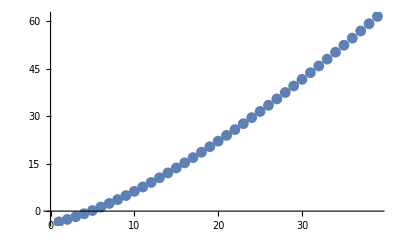

```mathematica
ListPlot[Log[wtbs[maxFun,a,b,g,d,maxFun+1]]]
```